```mathematica
myData[n_]:=ReadList[StringJoin["d:\\Triangle\\Data\\Summ357_UpTo_",ToString[n],".txt"],Number, RecordLists->True ]
```

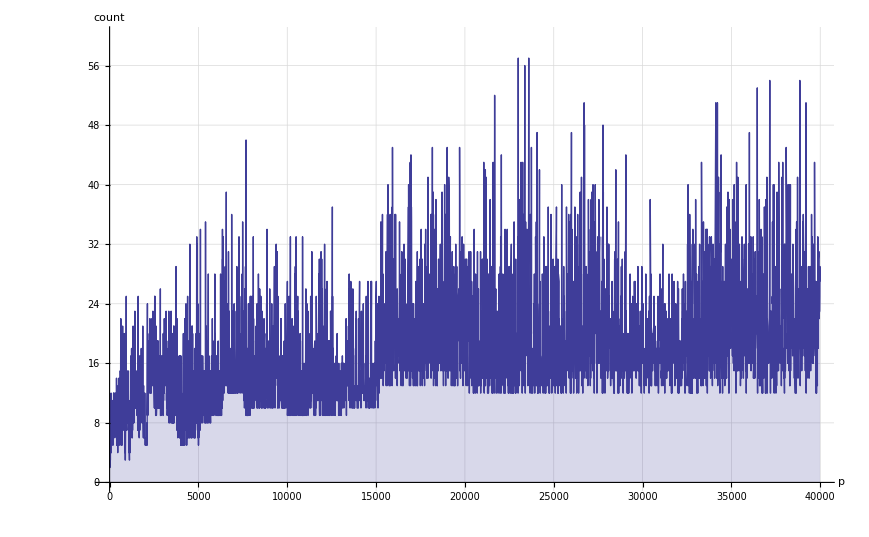

```mathematica
ListPlot[{myData[70]}, Joined->True,  Filling->Axis, PlotRange->{All,{0,60}}, GridLines->Automatic, AxesLabel->{"p","count"}]
```

```mathematica
Select[myData[70], #[[2]]>50&]
```

{{21673,52},{23003,57},{23369,56},{23593,57},{26711,51},{34123,51},{34213,51},{36457,53},{37159,54},{38851,54},{39199,51}}

```mathematica
FullSimplify[InterpolatingPolynomial[Take[myData[70],10],x]]
```

3+((-43+x) (-31+x) (-29+x) (-19+x) (-11+x) (38361505+x (-5944549+x (322197+x (-7439+62 x)))))/49816166400

```mathematica
Plot[3+((-43+x) (-31+x) (-29+x) (-19+x) (-11+x) (38361505+x (-5944549+x (322197+x (-7439+62 x)))))/49816166400, {x,1,40000}]
```

-Graphics-

```mathematica
myPrimes = Table[n[[1]], {n, myData[70]}]
```

{11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223,1229,1231,1237,1249,1259,1277,1279,1283,1289,1291,1297,1301,1303,1307,1319,1321,1327,1361,1367,1373,1381,1399,1409,1423,1427,1429,1433,1439,1447,1451,1453,1459,1471,1481,1483,1487,1489,1493,1499,1511,1523,1531,1543,1549,1553,1559,1567,1571,1579,1583,1597,1601,1607,1609,1613,1619,1621,1627,1637,1657,1663,1667,1669,1693,1697,1699,1709,1721,1723,1733,1741,1747,1753,1759,1777,1783,1787,1789,1801,1811,1823,1831,1847,1861,1867,1871,1873,1877,1879,1889,1901,1907,1913,1931,1933,1949,1951,1973,1979,1987,1993,1997,1999,2003,2011,2017,2027,2029,2039,2053,2063,2069,2081,2083,2087,2089,2099,2111,2113,2129,2131,2137,2141,2143,2153,2161,2179,2203,2207,2213,2221,2237,2239,2243,2251,2267,2269,2273,2281,2287,2293,2297,2309,2311,2333,2339,2341,2347,2351,2357,2371,2377,2381,2383,2389,2393,2399,2411,2417,2423,2437,2441,2447,2459,2467,2473,2477,2503,2521,2531,2539,2543,2549,2551,2557,2579,2591,2593,2609,2617,2621,2633,2647,2657,2659,2663,2671,2677,2683,2687,2689,2693,2699,2707,2711,2713,2719,2729,2731,2741,2749,2753,2767,2777,2789,2791,2797,2801,2803,2819,2833,2837,2843,2851,2857,2861,2879,2887,2897,2903,2909,2917,2927,2939,2953,2957,2963,2969,2971,2999,3001,3011,3019,3023,3037,3041,3049,3061,3067,3079,3083,3089,3109,3119,3121,3137,3163,3167,3169,3181,3187,3191,3203,3209,3217,3221,3229,3251,3253,3257,3259,3271,3299,3301,3307,3313,3319,3323,3329,3331,3343,3347,3359,3361,3371,3373,3389,3391,3407,3413,3433,3449,3457,3461,3463,3467,3469,3491,3499,3511,3517,3527,3529,3533,3539,3541,3547,3557,3559,3571,3581,3583,3593,3607,3613,3617,3623,3631,3637,3643,3659,3671,3673,3677,3691,3697,3701,3709,3719,3727,3733,3739,3761,3767,3769,3779,3793,3797,3803,3821,3823,3833,3847,3851,3853,3863,3877,3881,3889,3907,3911,3917,3919,3923,3929,3931,3943,3947,3967,3989,4001,4003,4007,4013,4019,4021,4027,4049,4051,4057,4073,4079,4091,4093,4099,4111,4127,4129,4133,4139,4153,4157,4159,4177,4201,4211,4217,4219,4229,4231,4241,4243,4253,4259,4261,4271,4273,4283,4289,4297,4327,4337,4339,4349,4357,4363,4373,4391,4397,4409,4421,4423,4441,4447,4451,4457,4463,4481,4483,4493,4507,4513,4517,4519,4523,4547,4549,4561,4567,4583,4591,4597,4603,4621,4637,4639,4643,4649,4651,4657,4663,4673,4679,4691,4703,4721,4723,4729,4733,4751,4759,4783,4787,4789,4793,4799,4801,4813,4817,4831,4861,4871,4877,4889,4903,4909,4919,4931,4933,4937,4943,4951,4957,4967,4969,4973,4987,4993,4999,5003,5009,5011,5021,5023,5039,5051,5059,5077,5081,5087,5099,5101,5107,5113,5119,5147,5153,5167,5171,5179,5189,5197,5209,5227,5231,5233,5237,5261,5273,5279,5281,5297,5303,5309,5323,5333,5347,5351,5381,5387,5393,5399,5407,5413,5417,5419,5431,5437,5441,5443,5449,5471,5477,5479,5483,5501,5503,5507,5519,5521,5527,5531,5557,5563,5569,5573,5581,5591,5623,5639,5641,5647,5651,5653,5657,5659,5669,5683,5689,5693,5701,5711,5717,5737,5741,5743,5749,5779,5783,5791,5801,5807,5813,5821,5827,5839,5843,5849,5851,5857,5861,5867,5869,5879,5881,5897,5903,5923,5927,5939,5953,5981,5987,6007,6011,6029,6037,6043,6047,6053,6067,6073,6079,6089,6091,6101,6113,6121,6131,6133,6143,6151,6163,6173,6197,6199,6203,6211,6217,6221,6229,6247,6257,6263,6269,6271,6277,6287,6299,6301,6311,6317,6323,6329,6337,6343,6353,6359,6361,6367,6373,6379,6389,6397,6421,6427,6449,6451,6469,6473,6481,6491,6521,6529,6547,6551,6553,6563,6569,6571,6577,6581,6599,6607,6619,6637,6653,6659,6661,6673,6679,6689,6691,6701,6703,6709,6719,6733,6737,6761,6763,6779,6781,6791,6793,6803,6823,6827,6829,6833,6841,6857,6863,6869,6871,6883,6899,6907,6911,6917,6947,6949,6959,6961,6967,6971,6977,6983,6991,6997,7001,7013,7019,7027,7039,7043,7057,7069,7079,7103,7109,7121,7127,7129,7151,7159,7177,7187,7193,7207,7211,7213,7219,7229,7237,7243,7247,7253,7283,7297,7307,7309,7321,7331,7333,7349,7351,7369,7393,7411,7417,7433,7451,7457,7459,7477,7481,7487,7489,7499,7507,7517,7523,7529,7537,7541,7547,7549,7559,7561,7573,7577,7583,7589,7591,7603,7607,7621,7639,7643,7649,7669,7673,7681,7687,7691,7699,7703,7717,7723,7727,7741,7753,7757,7759,7789,7793,7817,7823,7829,7841,7853,7867,7873,7877,7879,7883,7901,7907,7919,7927,7933,7937,7949,7951,7963,7993,8009,8011,8017,8039,8053,8059,8069,8081,8087,8089,8093,8101,8111,8117,8123,8147,8161,8167,8171,8179,8191,8209,8219,8221,8231,8233,8237,8243,8263,8269,8273,8287,8291,8293,8297,8311,8317,8329,8353,8363,8369,8377,8387,8389,8419,8423,8429,8431,8443,8447,8461,8467,8501,8513,8521,8527,8537,8539,8543,8563,8573,8581,8597,8599,8609,8623,8627,8629,8641,8647,8663,8669,8677,8681,8689,8693,8699,8707,8713,8719,8731,8737,8741,8747,8753,8761,8779,8783,8803,8807,8819,8821,8831,8837,8839,8849,8861,8863,8867,8887,8893,8923,8929,8933,8941,8951,8963,8969,8971,8999,9001,9007,9011,9013,9029,9041,9043,9049,9059,9067,9091,9103,9109,9127,9133,9137,9151,9157,9161,9173,9181,9187,9199,9203,9209,9221,9227,9239,9241,9257,9277,9281,9283,9293,9311,9319,9323,9337,9341,9343,9349,9371,9377,9391,9397,9403,9413,9419,9421,9431,9433,9437,9439,9461,9463,9467,9473,9479,9491,9497,9511,9521,9533,9539,9547,9551,9587,9601,9613,9619,9623,9629,9631,9643,9649,9661,9677,9679,9689,9697,9719,9721,9733,9739,9743,9749,9767,9769,9781,9787,9791,9803,9811,9817,9829,9833,9839,9851,9857,9859,9871,9883,9887,9901,9907,9923,9929,9931,9941,9949,9967,9973,10007,10009,10037,10039,10061,10067,10069,10079,10091,10093,10099,10103,10111,10133,10139,10141,10151,10159,10163,10169,10177,10181,10193,10211,10223,10243,10247,10253,10259,10267,10271,10273,10289,10301,10303,10313,10321,10331,10333,10337,10343,10357,10369,10391,10399,10427,10429,10433,10453,10457,10459,10463,10477,10487,10499,10501,10513,10529,10531,10559,10567,10589,10597,10601,10607,10613,10627,10631,10639,10651,10657,10663,10667,10687,10691,10709,10711,10723,10729,10733,10739,10753,10771,10781,10789,10799,10831,10837,10847,10853,10859,10861,10867,10883,10889,10891,10903,10909,10937,10939,10949,10957,10973,10979,10987,10993,11003,11027,11047,11057,11059,11069,11071,11083,11087,11093,11113,11117,11119,11131,11149,11159,11161,11171,11173,11177,11197,11213,11239,11243,11251,11257,11261,11273,11279,11287,11299,11311,11317,11321,11329,11351,11353,11369,11383,11393,11399,11411,11423,11437,11443,11447,11467,11471,11483,11489,11491,11497,11503,11519,11527,11549,11551,11579,11587,11593,11597,11617,11621,11633,11657,11677,11681,11689,11699,11701,11717,11719,11731,11743,11777,11779,11783,11789,11801,11807,11813,11821,11827,11831,11833,11839,11863,11867,11887,11897,11903,11909,11923,11927,11933,11939,11941,11953,11959,11969,11971,11981,11987,12007,12011,12037,12041,12043,12049,12071,12073,12097,12101,12107,12109,12113,12119,12143,12149,12157,12161,12163,12197,12203,12211,12227,12239,12241,12251,12253,12263,12269,12277,12281,12289,12301,12323,12329,12343,12347,12373,12377,12379,12391,12401,12409,12413,12421,12433,12437,12451,12457,12473,12479,12487,12491,12497,12503,12511,12517,12527,12539,12541,12547,12553,12569,12577,12583,12589,12601,12611,12613,12619,12637,12641,12647,12653,12659,12671,12689,12697,12703,12713,12721,12739,12743,12757,12763,12781,12791,12799,12809,12821,12823,12829,12841,12853,12889,12893,12899,12907,12911,12917,12919,12923,12941,12953,12959,12967,12973,12979,12983,13001,13003,13007,13009,13033,13037,13043,13049,13063,13093,13099,13103,13109,13121,13127,13147,13151,13159,13163,13171,13177,13183,13187,13217,13219,13229,13241,13249,13259,13267,13291,13297,13309,13313,13327,13331,13337,13339,13367,13381,13397,13399,13411,13417,13421,13441,13451,13457,13463,13469,13477,13487,13499,13513,13523,13537,13553,13567,13577,13591,13597,13613,13619,13627,13633,13649,13669,13679,13681,13687,13691,13693,13697,13709,13711,13721,13723,13729,13751,13757,13759,13763,13781,13789,13799,13807,13829,13831,13841,13859,13873,13877,13879,13883,13901,13903,13907,13913,13921,13931,13933,13963,13967,13997,13999,14009,14011,14029,14033,14051,14057,14071,14081,14083,14087,14107,14143,14149,14153,14159,14173,14177,14197,14207,14221,14243,14249,14251,14281,14293,14303,14321,14323,14327,14341,14347,14369,14387,14389,14401,14407,14411,14419,14423,14431,14437,14447,14449,14461,14479,14489,14503,14519,14533,14537,14543,14549,14551,14557,14561,14563,14591,14593,14621,14627,14629,14633,14639,14653,14657,14669,14683,14699,14713,14717,14723,14731,14737,14741,14747,14753,14759,14767,14771,14779,14783,14797,14813,14821,14827,14831,14843,14851,14867,14869,14879,14887,14891,14897,14923,14929,14939,14947,14951,14957,14969,14983,15013,15017,15031,15053,15061,15073,15077,15083,15091,15101,15107,15121,15131,15137,15139,15149,15161,15173,15187,15193,15199,15217,15227,15233,15241,15259,15263,15269,15271,15277,15287,15289,15299,15307,15313,15319,15329,15331,15349,15359,15361,15373,15377,15383,15391,15401,15413,15427,15439,15443,15451,15461,15467,15473,15493,15497,15511,15527,15541,15551,15559,15569,15581,15583,15601,15607,15619,15629,15641,15643,15647,15649,15661,15667,15671,15679,15683,15727,15731,15733,15737,15739,15749,15761,15767,15773,15787,15791,15797,15803,15809,15817,15823,15859,15877,15881,15887,15889,15901,15907,15913,15919,15923,15937,15959,15971,15973,15991,16001,16007,16033,16057,16061,16063,16067,16069,16073,16087,16091,16097,16103,16111,16127,16139,16141,16183,16187,16189,16193,16217,16223,16229,16231,16249,16253,16267,16273,16301,16319,16333,16339,16349,16361,16363,16369,16381,16411,16417,16421,16427,16433,16447,16451,16453,16477,16481,16487,16493,16519,16529,16547,16553,16561,16567,16573,16603,16607,16619,16631,16633,16649,16651,16657,16661,16673,16691,16693,16699,16703,16729,16741,16747,16759,16763,16787,16811,16823,16829,16831,16843,16871,16879,16883,16889,16901,16903,16921,16927,16931,16937,16943,16963,16979,16981,16987,16993,17011,17021,17027,17029,17033,17041,17047,17053,17077,17093,17099,17107,17117,17123,17137,17159,17167,17183,17189,17191,17203,17207,17209,17231,17239,17257,17291,17293,17299,17317,17321,17327,17333,17341,17351,17359,17377,17383,17387,17389,17393,17401,17417,17419,17431,17443,17449,17467,17471,17477,17483,17489,17491,17497,17509,17519,17539,17551,17569,17573,17579,17581,17597,17599,17609,17623,17627,17657,17659,17669,17681,17683,17707,17713,17729,17737,17747,17749,17761,17783,17789,17791,17807,17827,17837,17839,17851,17863,17881,17891,17903,17909,17911,17921,17923,17929,17939,17957,17959,17971,17977,17981,17987,17989,18013,18041,18043,18047,18049,18059,18061,18077,18089,18097,18119,18121,18127,18131,18133,18143,18149,18169,18181,18191,18199,18211,18217,18223,18229,18233,18251,18253,18257,18269,18287,18289,18301,18307,18311,18313,18329,18341,18353,18367,18371,18379,18397,18401,18413,18427,18433,18439,18443,18451,18457,18461,18481,18493,18503,18517,18521,18523,18539,18541,18553,18583,18587,18593,18617,18637,18661,18671,18679,18691,18701,18713,18719,18731,18743,18749,18757,18773,18787,18793,18797,18803,18839,18859,18869,18899,18911,18913,18917,18919,18947,18959,18973,18979,19001,19009,19013,19031,19037,19051,19069,19073,19079,19081,19087,19121,19139,19141,19157,19163,19181,19183,19207,19211,19213,19219,19231,19237,19249,19259,19267,19273,19289,19301,19309,19319,19333,19373,19379,19381,19387,19391,19403,19417,19421,19423,19427,19429,19433,19441,19447,19457,19463,19469,19471,19477,19483,19489,19501,19507,19531,19541,19543,19553,19559,19571,19577,19583,19597,19603,19609,19661,19681,19687,19697,19699,19709,19717,19727,19739,19751,19753,19759,19763,19777,19793,19801,19813,19819,19841,19843,19853,19861,19867,19889,19891,19913,19919,19927,19937,19949,19961,19963,19973,19979,19991,19993,19997,20011,20021,20023,20029,20047,20051,20063,20071,20089,20101,20107,20113,20117,20123,20129,20143,20147,20149,20161,20173,20177,20183,20201,20219,20231,20233,20249,20261,20269,20287,20297,20323,20327,20333,20341,20347,20353,20357,20359,20369,20389,20393,20399,20407,20411,20431,20441,20443,20477,20479,20483,20507,20509,20521,20533,20543,20549,20551,20563,20593,20599,20611,20627,20639,20641,20663,20681,20693,20707,20717,20719,20731,20743,20747,20749,20753,20759,20771,20773,20789,20807,20809,20849,20857,20873,20879,20887,20897,20899,20903,20921,20929,20939,20947,20959,20963,20981,20983,21001,21011,21013,21017,21019,21023,21031,21059,21061,21067,21089,21101,21107,21121,21139,21143,21149,21157,21163,21169,21179,21187,21191,21193,21211,21221,21227,21247,21269,21277,21283,21313,21317,21319,21323,21341,21347,21377,21379,21383,21391,21397,21401,21407,21419,21433,21467,21481,21487,21491,21493,21499,21503,21517,21521,21523,21529,21557,21559,21563,21569,21577,21587,21589,21599,21601,21611,21613,21617,21647,21649,21661,21673,21683,21701,21713,21727,21737,21739,21751,21757,21767,21773,21787,21799,21803,21817,21821,21839,21841,21851,21859,21863,21871,21881,21893,21911,21929,21937,21943,21961,21977,21991,21997,22003,22013,22027,22031,22037,22039,22051,22063,22067,22073,22079,22091,22093,22109,22111,22123,22129,22133,22147,22153,22157,22159,22171,22189,22193,22229,22247,22259,22271,22273,22277,22279,22283,22291,22303,22307,22343,22349,22367,22369,22381,22391,22397,22409,22433,22441,22447,22453,22469,22481,22483,22501,22511,22531,22541,22543,22549,22567,22571,22573,22613,22619,22621,22637,22639,22643,22651,22669,22679,22691,22697,22699,22709,22717,22721,22727,22739,22741,22751,22769,22777,22783,22787,22807,22811,22817,22853,22859,22861,22871,22877,22901,22907,22921,22937,22943,22961,22963,22973,22993,23003,23011,23017,23021,23027,23029,23039,23041,23053,23057,23059,23063,23071,23081,23087,23099,23117,23131,23143,23159,23167,23173,23189,23197,23201,23203,23209,23227,23251,23269,23279,23291,23293,23297,23311,23321,23327,23333,23339,23357,23369,23371,23399,23417,23431,23447,23459,23473,23497,23509,23531,23537,23539,23549,23557,23561,23563,23567,23581,23593,23599,23603,23609,23623,23627,23629,23633,23663,23669,23671,23677,23687,23689,23719,23741,23743,23747,23753,23761,23767,23773,23789,23801,23813,23819,23827,23831,23833,23857,23869,23873,23879,23887,23893,23899,23909,23911,23917,23929,23957,23971,23977,23981,23993,24001,24007,24019,24023,24029,24043,24049,24061,24071,24077,24083,24091,24097,24103,24107,24109,24113,24121,24133,24137,24151,24169,24179,24181,24197,24203,24223,24229,24239,24247,24251,24281,24317,24329,24337,24359,24371,24373,24379,24391,24407,24413,24419,24421,24439,24443,24469,24473,24481,24499,24509,24517,24527,24533,24547,24551,24571,24593,24611,24623,24631,24659,24671,24677,24683,24691,24697,24709,24733,24749,24763,24767,24781,24793,24799,24809,24821,24841,24847,24851,24859,24877,24889,24907,24917,24919,24923,24943,24953,24967,24971,24977,24979,24989,25013,25031,25033,25037,25057,25073,25087,25097,25111,25117,25121,25127,25147,25153,25163,25169,25171,25183,25189,25219,25229,25237,25243,25247,25253,25261,25301,25303,25307,25309,25321,25339,25343,25349,25357,25367,25373,25391,25409,25411,25423,25439,25447,25453,25457,25463,25469,25471,25523,25537,25541,25561,25577,25579,25583,25589,25601,25603,25609,25621,25633,25639,25643,25657,25667,25673,25679,25693,25703,25717,25733,25741,25747,25759,25763,25771,25793,25799,25801,25819,25841,25847,25849,25867,25873,25889,25903,25913,25919,25931,25933,25939,25943,25951,25969,25981,25997,25999,26003,26017,26021,26029,26041,26053,26083,26099,26107,26111,26113,26119,26141,26153,26161,26171,26177,26183,26189,26203,26209,26227,26237,26249,26251,26261,26263,26267,26293,26297,26309,26317,26321,26339,26347,26357,26371,26387,26393,26399,26407,26417,26423,26431,26437,26449,26459,26479,26489,26497,26501,26513,26539,26557,26561,26573,26591,26597,26627,26633,26641,26647,26669,26681,26683,26687,26693,26699,26701,26711,26713,26717,26723,26729,26731,26737,26759,26777,26783,26801,26813,26821,26833,26839,26849,26861,26863,26879,26881,26891,26893,26903,26921,26927,26947,26951,26953,26959,26981,26987,26993,27011,27017,27031,27043,27059,27061,27067,27073,27077,27091,27103,27107,27109,27127,27143,27179,27191,27197,27211,27239,27241,27253,27259,27271,27277,27281,27283,27299,27329,27337,27361,27367,27397,27407,27409,27427,27431,27437,27449,27457,27479,27481,27487,27509,27527,27529,27539,27541,27551,27581,27583,27611,27617,27631,27647,27653,27673,27689,27691,27697,27701,27733,27737,27739,27743,27749,27751,27763,27767,27773,27779,27791,27793,27799,27803,27809,27817,27823,27827,27847,27851,27883,27893,27901,27917,27919,27941,27943,27947,27953,27961,27967,27983,27997,28001,28019,28027,28031,28051,28057,28069,28081,28087,28097,28099,28109,28111,28123,28151,28163,28181,28183,28201,28211,28219,28229,28277,28279,28283,28289,28297,28307,28309,28319,28349,28351,28387,28393,28403,28409,28411,28429,28433,28439,28447,28463,28477,28493,28499,28513,28517,28537,28541,28547,28549,28559,28571,28573,28579,28591,28597,28603,28607,28619,28621,28627,28631,28643,28649,28657,28661,28663,28669,28687,28697,28703,28711,28723,28729,28751,28753,28759,28771,28789,28793,28807,28813,28817,28837,28843,28859,28867,28871,28879,28901,28909,28921,28927,28933,28949,28961,28979,29009,29017,29021,29023,29027,29033,29059,29063,29077,29101,29123,29129,29131,29137,29147,29153,29167,29173,29179,29191,29201,29207,29209,29221,29231,29243,29251,29269,29287,29297,29303,29311,29327,29333,29339,29347,29363,29383,29387,29389,29399,29401,29411,29423,29429,29437,29443,29453,29473,29483,29501,29527,29531,29537,29567,29569,29573,29581,29587,29599,29611,29629,29633,29641,29663,29669,29671,29683,29717,29723,29741,29753,29759,29761,29789,29803,29819,29833,29837,29851,29863,29867,29873,29879,29881,29917,29921,29927,29947,29959,29983,29989,30011,30013,30029,30047,30059,30071,30089,30091,30097,30103,30109,30113,30119,30133,30137,30139,30161,30169,30181,30187,30197,30203,30211,30223,30241,30253,30259,30269,30271,30293,30307,30313,30319,30323,30341,30347,30367,30389,30391,30403,30427,30431,30449,30467,30469,30491,30493,30497,30509,30517,30529,30539,30553,30557,30559,30577,30593,30631,30637,30643,30649,30661,30671,30677,30689,30697,30703,30707,30713,30727,30757,30763,30773,30781,30803,30809,30817,30829,30839,30841,30851,30853,30859,30869,30871,30881,30893,30911,30931,30937,30941,30949,30971,30977,30983,31013,31019,31033,31039,31051,31063,31069,31079,31081,31091,31121,31123,31139,31147,31151,31153,31159,31177,31181,31183,31189,31193,31219,31223,31231,31237,31247,31249,31253,31259,31267,31271,31277,31307,31319,31321,31327,31333,31337,31357,31379,31387,31391,31393,31397,31469,31477,31481,31489,31511,31513,31517,31531,31541,31543,31547,31567,31573,31583,31601,31607,31627,31643,31649,31657,31663,31667,31687,31699,31721,31723,31727,31729,31741,31751,31769,31771,31793,31799,31817,31847,31849,31859,31873,31883,31891,31907,31957,31963,31973,31981,31991,32003,32009,32027,32029,32051,32057,32059,32063,32069,32077,32083,32089,32099,32117,32119,32141,32143,32159,32173,32183,32189,32191,32203,32213,32233,32237,32251,32257,32261,32297,32299,32303,32309,32321,32323,32327,32341,32353,32359,32363,32369,32371,32377,32381,32401,32411,32413,32423,32429,32441,32443,32467,32479,32491,32497,32503,32507,32531,32533,32537,32561,32563,32569,32573,32579,32587,32603,32609,32611,32621,32633,32647,32653,32687,32693,32707,32713,32717,32719,32749,32771,32779,32783,32789,32797,32801,32803,32831,32833,32839,32843,32869,32887,32909,32911,32917,32933,32939,32941,32957,32969,32971,32983,32987,32993,32999,33013,33023,33029,33037,33049,33053,33071,33073,33083,33091,33107,33113,33119,33149,33151,33161,33179,33181,33191,33199,33203,33211,33223,33247,33287,33289,33301,33311,33317,33329,33331,33343,33347,33349,33353,33359,33377,33391,33403,33409,33413,33427,33457,33461,33469,33479,33487,33493,33503,33521,33529,33533,33547,33563,33569,33577,33581,33587,33589,33599,33601,33613,33617,33619,33623,33629,33637,33641,33647,33679,33703,33713,33721,33739,33749,33751,33757,33767,33769,33773,33791,33797,33809,33811,33827,33829,33851,33857,33863,33871,33889,33893,33911,33923,33931,33937,33941,33961,33967,33997,34019,34031,34033,34039,34057,34061,34123,34127,34129,34141,34147,34157,34159,34171,34183,34211,34213,34217,34231,34253,34259,34261,34267,34273,34283,34297,34301,34303,34313,34319,34327,34337,34351,34361,34367,34369,34381,34403,34421,34429,34439,34457,34469,34471,34483,34487,34499,34501,34511,34513,34519,34537,34543,34549,34583,34589,34591,34603,34607,34613,34631,34649,34651,34667,34673,34679,34687,34693,34703,34721,34729,34739,34747,34757,34759,34763,34781,34807,34819,34841,34843,34847,34849,34871,34877,34883,34897,34913,34919,34939,34949,34961,34963,34981,35023,35027,35051,35053,35059,35069,35081,35083,35089,35099,35107,35111,35117,35129,35141,35149,35153,35159,35171,35201,35221,35227,35251,35257,35267,35279,35281,35291,35311,35317,35323,35327,35339,35353,35363,35381,35393,35401,35407,35419,35423,35437,35447,35449,35461,35491,35507,35509,35521,35527,35531,35533,35537,35543,35569,35573,35591,35593,35597,35603,35617,35671,35677,35729,35731,35747,35753,35759,35771,35797,35801,35803,35809,35831,35837,35839,35851,35863,35869,35879,35897,35899,35911,35923,35933,35951,35963,35969,35977,35983,35993,35999,36007,36011,36013,36017,36037,36061,36067,36073,36083,36097,36107,36109,36131,36137,36151,36161,36187,36191,36209,36217,36229,36241,36251,36263,36269,36277,36293,36299,36307,36313,36319,36341,36343,36353,36373,36383,36389,36433,36451,36457,36467,36469,36473,36479,36493,36497,36523,36527,36529,36541,36551,36559,36563,36571,36583,36587,36599,36607,36629,36637,36643,36653,36671,36677,36683,36691,36697,36709,36713,36721,36739,36749,36761,36767,36779,36781,36787,36791,36793,36809,36821,36833,36847,36857,36871,36877,36887,36899,36901,36913,36919,36923,36929,36931,36943,36947,36973,36979,36997,37003,37013,37019,37021,37039,37049,37057,37061,37087,37097,37117,37123,37139,37159,37171,37181,37189,37199,37201,37217,37223,37243,37253,37273,37277,37307,37309,37313,37321,37337,37339,37357,37361,37363,37369,37379,37397,37409,37423,37441,37447,37463,37483,37489,37493,37501,37507,37511,37517,37529,37537,37547,37549,37561,37567,37571,37573,37579,37589,37591,37607,37619,37633,37643,37649,37657,37663,37691,37693,37699,37717,37747,37781,37783,37799,37811,37813,37831,37847,37853,37861,37871,37879,37889,37897,37907,37951,37957,37963,37967,37987,37991,37993,37997,38011,38039,38047,38053,38069,38083,38113,38119,38149,38153,38167,38177,38183,38189,38197,38201,38219,38231,38237,38239,38261,38273,38281,38287,38299,38303,38317,38321,38327,38329,38333,38351,38371,38377,38393,38431,38447,38449,38453,38459,38461,38501,38543,38557,38561,38567,38569,38593,38603,38609,38611,38629,38639,38651,38653,38669,38671,38677,38693,38699,38707,38711,38713,38723,38729,38737,38747,38749,38767,38783,38791,38803,38821,38833,38839,38851,38861,38867,38873,38891,38903,38917,38921,38923,38933,38953,38959,38971,38977,38993,39019,39023,39041,39043,39047,39079,39089,39097,39103,39107,39113,39119,39133,39139,39157,39161,39163,39181,39191,39199,39209,39217,39227,39229,39233,39239,39241,39251,39293,39301,39313,39317,39323,39341,39343,39359,39367,39371,39373,39383,39397,39409,39419,39439,39443,39451,39461,39499,39503,39509,39511,39521,39541,39551,39563,39569,39581,39607,39619,39623,39631,39659,39667,39671,39679,39703,39709,39719,39727,39733,39749,39761,39769,39779,39791,39799,39821,39827,39829,39839,39841,39847,39857,39863,39869,39877,39883,39887,39901,39929,39937,39953,39971,39979,39983,39989}

```mathematica
myValues = Accumulate[Table[n[[2]], {n, myData[70]}]]
```

{3,8,10,13,17,20,23,29,36,39,47,57,62,69,74,80,87,91,103,107,112,119,124,131,136,141,148,155,164,173,182,193,201,207,215,224,232,239,244,250,261,268,279,290,302,312,320,331,343,351,359,368,376,383,390,398,406,412,421,433,445,455,466,477,487,497,507,516,523,535,542,550,564,574,582,587,593,598,605,614,624,635,643,647,656,663,675,681,694,706,718,730,743,757,769,776,781,786,793,802,811,821,833,845,855,870,884,896,909,922,944,951,970,977,982,990,1005,1014,1022,1034,1040,1045,1058,1076,1087,1108,1121,1133,1145,1155,1165,1173,1181,1191,1198,1205,1219,1239,1253,1262,1270,1281,1291,1297,1302,1306,1311,1314,1317,1320,1330,1339,1359,1372,1397,1410,1421,1429,1436,1443,1454,1462,1471,1485,1496,1508,1520,1530,1544,1559,1572,1583,1596,1606,1617,1625,1632,1639,1644,1648,1656,1660,1663,1669,1679,1690,1694,1702,1711,1726,1735,1744,1761,1770,1781,1789,1798,1809,1827,1835,1841,1848,1854,1868,1878,1885,1894,1904,1912,1920,1935,1956,1964,1979,1987,1998,2008,2019,2032,2055,2067,2083,2101,2111,2123,2133,2145,2155,2165,2178,2193,2204,2216,2227,2238,2251,2265,2278,2287,2296,2305,2315,2324,2333,2342,2350,2357,2377,2384,2409,2416,2423,2432,2445,2452,2459,2465,2471,2478,2495,2502,2509,2518,2530,2542,2551,2561,2570,2582,2595,2604,2622,2632,2645,2658,2668,2676,2686,2694,2705,2726,2736,2746,2754,2762,2770,2776,2788,2801,2807,2814,2820,2826,2832,2844,2850,2856,2862,2868,2873,2878,2884,2890,2896,2902,2908,2914,2919,2925,2930,2935,2942,2947,2955,2962,2986,2995,3006,3018,3027,3038,3054,3066,3079,3098,3113,3126,3141,3161,3178,3193,3206,3228,3240,3254,3268,3280,3297,3309,3327,3343,3355,3368,3382,3397,3411,3427,3440,3454,3476,3495,3511,3527,3540,3559,3574,3597,3614,3630,3644,3660,3677,3694,3706,3716,3736,3761,3771,3796,3810,3821,3841,3850,3859,3868,3889,3903,3912,3922,3933,3944,3955,3970,3982,3993,4004,4023,4040,4052,4062,4080,4099,4109,4126,4145,4155,4167,4177,4187,4197,4208,4225,4237,4253,4263,4273,4284,4294,4304,4314,4340,4349,4358,4369,4382,4391,4403,4414,4427,4444,4457,4467,4479,4489,4506,4517,4526,4535,4544,4564,4575,4595,4614,4626,4638,4660,4681,4697,4710,4730,4745,4762,4778,4800,4813,4836,4850,4866,4877,4889,4899,4912,4922,4932,4941,4954,4963,4973,4991,5001,5020,5034,5045,5056,5065,5088,5096,5108,5123,5133,5143,5154,5170,5178,5191,5202,5221,5235,5250,5260,5283,5295,5303,5320,5328,5338,5353,5366,5377,5397,5412,5420,5429,5447,5455,5464,5473,5481,5493,5501,5522,5539,5560,5568,5577,5591,5602,5613,5627,5638,5649,5660,5672,5683,5692,5701,5710,5739,5750,5759,5769,5778,5785,5807,5825,5837,5851,5857,5865,5876,5886,5899,5910,5925,5940,5950,5958,5975,5985,5995,6001,6007,6015,6021,6038,6044,6050,6055,6060,6077,6082,6087,6092,6104,6109,6114,6119,6124,6129,6134,6139,6144,6149,6160,6167,6179,6199,6204,6209,6216,6226,6238,6253,6271,6276,6298,6306,6314,6335,6342,6351,6358,6368,6381,6392,6416,6433,6440,6445,6452,6474,6490,6500,6525,6531,6549,6556,6575,6585,6591,6597,6604,6611,6621,6627,6633,6646,6654,6686,6693,6699,6710,6719,6727,6738,6755,6761,6769,6775,6786,6807,6813,6819,6829,6850,6858,6870,6890,6902,6910,6920,6935,6943,6950,6956,6967,6976,6982,7000,7006,7012,7018,7029,7044,7050,7058,7066,7086,7097,7105,7138,7171,7181,7189,7221,7230,7239,7246,7256,7280,7286,7300,7309,7318,7327,7332,7339,7345,7355,7362,7381,7401,7420,7429,7442,7449,7458,7466,7477,7511,7519,7531,7545,7562,7570,7580,7589,7604,7613,7625,7633,7644,7661,7672,7686,7701,7712,7721,7731,7746,7761,7772,7780,7793,7804,7815,7823,7858,7873,7891,7911,7919,7927,7938,7948,7969,7979,7988,8000,8012,8020,8029,8048,8063,8071,8079,8093,8103,8131,8141,8153,8166,8174,8191,8204,8213,8222,8232,8241,8253,8261,8273,8282,8290,8299,8308,8323,8333,8343,8358,8375,8384,8393,8403,8425,8439,8453,8465,8477,8486,8505,8519,8536,8546,8558,8568,8580,8589,8603,8613,8623,8633,8643,8671,8688,8708,8721,8730,8739,8756,8766,8775,8785,8795,8804,8814,8831,8842,8851,8860,8871,8880,8899,8908,8917,8926,8935,8946,8961,8971,8980,8989,9003,9015,9024,9033,9042,9070,9083,9092,9108,9135,9147,9158,9167,9176,9189,9199,9214,9231,9241,9255,9289,9303,9333,9344,9361,9381,9414,9432,9453,9482,9494,9506,9533,9553,9567,9581,9595,9608,9637,9651,9670,9694,9733,9749,9765,9778,9797,9810,9834,9855,9870,9883,9899,9911,9925,9945,9976,9991,10003,10021,10036,10059,10078,10090,10105,10121,10133,10145,10159,10174,10192,10207,10219,10233,10250,10265,10277,10295,10331,10343,10357,10371,10387,10399,10422,10436,10451,10463,10477,10491,10503,10523,10536,10553,10572,10596,10608,10628,10650,10673,10693,10706,10718,10732,10747,10761,10777,10789,10807,10836,10861,10880,10892,10910,10930,10943,10955,10972,10996,11018,11043,11059,11092,11105,11120,11134,11159,11182,11196,11208,11221,11236,11251,11271,11289,11304,11320,11332,11360,11376,11393,11411,11446,11462,11478,11491,11508,11529,11541,11555,11569,11588,11611,11622,11636,11649,11661,11673,11683,11702,11728,11741,11754,11771,11800,11810,11820,11866,11875,11888,11898,11907,11922,11938,11947,11956,11974,11983,11992,12001,12010,12034,12043,12057,12078,12095,12109,12131,12141,12162,12177,12186,12199,12224,12243,12267,12290,12300,12325,12336,12346,12361,12373,12398,12408,12418,12428,12444,12454,12477,12510,12520,12542,12553,12566,12576,12586,12597,12614,12625,12640,12652,12668,12683,12702,12720,12735,12748,12769,12786,12801,12814,12834,12844,12866,12890,12909,12923,12933,12943,12955,12966,12994,13009,13025,13049,13059,13073,13083,13097,13123,13141,13157,13171,13196,13207,13221,13233,13243,13255,13266,13276,13299,13318,13329,13340,13352,13368,13378,13391,13407,13418,13429,13448,13464,13475,13497,13507,13521,13535,13554,13574,13584,13600,13616,13634,13644,13655,13665,13676,13688,13703,13721,13736,13748,13772,13787,13802,13836,13852,13862,13872,13883,13898,13909,13928,13940,13951,13962,13972,13984,13995,14012,14028,14054,14066,14077,14088,14107,14117,14132,14143,14159,14169,14193,14205,14223,14238,14249,14260,14270,14281,14293,14303,14323,14344,14359,14370,14385,14398,14417,14446,14457,14473,14495,14505,14522,14536,14550,14563,14579,14596,14618,14650,14668,14682,14706,14721,14735,14764,14795,14816,14841,14856,14874,14891,14901,14926,14936,14950,14968,14980,14997,15014,15031,15042,15052,15064,15080,15092,15104,15115,15126,15148,15161,15183,15194,15205,15216,15226,15243,15253,15268,15285,15296,15306,15317,15327,15337,15348,15358,15370,15382,15392,15407,15426,15443,15453,15463,15479,15494,15504,15515,15539,15551,15564,15579,15589,15605,15620,15631,15642,15656,15683,15692,15703,15712,15724,15738,15750,15762,15782,15797,15822,15833,15843,15852,15863,15872,15888,15902,15911,15924,15957,15966,15979,15997,16008,16027,16046,16064,16083,16093,16102,16124,16138,16150,16163,16179,16190,16206,16227,16237,16246,16260,16277,16286,16297,16308,16336,16345,16374,16383,16407,16417,16443,16456,16489,16499,16509,16522,16531,16555,16576,16601,16618,16631,16641,16664,16673,16684,16694,16704,16716,16733,16746,16755,16768,16787,16806,16826,16836,16846,16865,16874,16884,16893,16903,16918,16929,16938,16949,16958,16968,17001,17010,17019,17030,17039,17049,17058,17068,17077,17093,17103,17116,17129,17144,17153,17165,17178,17204,17216,17234,17243,17254,17263,17276,17294,17318,17328,17351,17361,17373,17390,17413,17422,17431,17441,17458,17468,17479,17494,17505,17519,17530,17543,17553,17573,17584,17599,17624,17634,17651,17664,17675,17692,17723,17744,17772,17784,17798,17811,17829,17842,17854,17865,17875,17886,17902,17913,17922,17931,17949,17968,17981,17990,18005,18014,18029,18039,18050,18075,18090,18110,18121,18133,18150,18164,18179,18190,18201,18213,18241,18258,18270,18285,18306,18336,18346,18355,18381,18393,18405,18424,18434,18443,18463,18476,18507,18518,18542,18567,18589,18619,18646,18665,18681,18692,18718,18729,18738,18757,18778,18790,18808,18817,18830,18842,18858,18885,18917,18928,18937,18953,18964,18980,18989,19005,19014,19026,19047,19073,19088,19106,19133,19151,19174,19183,19193,19206,19220,19238,19255,19264,19283,19297,19315,19334,19343,19362,19373,19382,19397,19415,19431,19442,19452,19475,19492,19503,19526,19547,19556,19569,19589,19600,19616,19635,19650,19687,19705,19727,19752,19769,19778,19796,19813,19823,19834,19847,19858,19869,19880,19890,19905,19916,19932,19941,19951,19960,19974,19988,20001,20012,20029,20043,20055,20066,20077,20097,20108,20122,20133,20144,20157,20169,20178,20194,20204,20216,20229,20240,20249,20262,20274,20289,20300,20311,20322,20335,20346,20355,20366,20379,20390,20401,20410,20426,20436,20449,20460,20477,20487,20498,20510,20521,20532,20546,20558,20574,20585,20601,20611,20622,20635,20646,20660,20671,20683,20695,20707,20720,20735,20757,20773,20782,20803,20816,20834,20847,20861,20880,20893,20908,20921,20935,20950,20962,20974,21000,21011,21039,21056,21069,21087,21097,21114,21127,21154,21174,21191,21203,21216,21227,21237,21247,21259,21276,21294,21306,21332,21342,21352,21362,21376,21388,21406,21418,21430,21440,21450,21461,21474,21484,21497,21508,21520,21537,21554,21576,21588,21600,21612,21635,21648,21660,21671,21684,21696,21706,21716,21726,21737,21749,21759,21771,21793,21804,21818,21835,21858,21885,21896,21908,21922,21935,21947,21957,21972,21984,22007,22024,22037,22049,22062,22075,22089,22101,22125,22138,22150,22163,22174,22187,22199,22210,22222,22236,22252,22268,22283,22295,22308,22319,22332,22342,22367,22380,22397,22409,22426,22437,22449,22462,22474,22501,22512,22532,22542,22552,22564,22577,22588,22598,22610,22620,22634,22647,22657,22670,22682,22697,22723,22736,22762,22789,22812,22836,22863,22876,22888,22900,22910,22922,22934,22948,22961,22973,22984,22997,23013,23023,23033,23046,23058,23072,23085,23097,23110,23126,23136,23149,23160,23172,23191,23205,23228,23255,23269,23293,23306,23330,23341,23364,23377,23389,23412,23422,23437,23449,23466,23480,23493,23518,23530,23545,23565,23579,23594,23608,23627,23650,23665,23681,23716,23744,23764,23783,23801,23820,23845,23859,23883,23901,23922,23947,23983,24006,24020,24045,24073,24088,24101,24115,24132,24151,24166,24186,24210,24234,24253,24272,24288,24308,24326,24342,24364,24395,24408,24425,24454,24468,24490,24503,24530,24566,24585,24599,24620,24641,24657,24697,24713,24732,24759,24776,24789,24802,24817,24832,24850,24863,24886,24902,24938,24953,24979,24992,25006,25024,25041,25061,25089,25109,25128,25141,25166,25203,25220,25265,25289,25305,25335,25351,25366,25394,25414,25444,25465,25484,25520,25543,25575,25594,25614,25628,25664,25680,25701,25720,25739,25758,25775,25788,25811,25837,25854,25870,25890,25908,25930,25952,25970,25987,26006,26041,26067,26082,26102,26119,26138,26162,26183,26196,26222,26237,26265,26283,26314,26332,26355,26370,26389,26408,26421,26434,26451,26471,26502,26520,26540,26572,26587,26602,26622,26640,26670,26694,26714,26730,26746,26770,26784,26802,26817,26833,26855,26871,26885,26900,26915,26941,26974,27011,27026,27066,27085,27112,27125,27145,27168,27185,27204,27247,27279,27303,27316,27347,27391,27406,27428,27465,27500,27515,27537,27553,27575,27594,27616,27631,27645,27669,27685,27698,27722,27741,27758,27771,27792,27807,27829,27849,27865,27878,27891,27906,27920,27947,27960,27984,28004,28030,28043,28074,28087,28111,28140,28157,28173,28188,28204,28233,28253,28271,28295,28319,28338,28353,28380,28395,28417,28444,28474,28498,28514,28527,28542,28559,28579,28613,28631,28652,28667,28690,28711,28741,28754,28773,28790,28811,28835,28851,28866,28885,28899,28920,28936,28949,28981,29001,29017,29036,29054,29088,29114,29138,29154,29169,29188,29202,29228,29257,29276,29297,29323,29341,29355,29396,29418,29435,29452,29473,29497,29517,29543,29571,29590,29608,29624,29651,29675,29692,29719,29742,29769,29805,29819,29845,29869,29905,29932,29950,29969,29987,30032,30057,30080,30095,30129,30168,30186,30222,30235,30253,30274,30288,30302,30317,30331,30365,30381,30401,30415,30434,30459,30472,30501,30539,30558,30573,30596,30617,30632,30645,30660,30673,30694,30710,30736,30760,30775,30790,30820,30836,30855,30877,30905,30921,30937,30957,30983,31015,31030,31047,31063,31079,31099,31129,31168,31183,31209,31231,31258,31277,31295,31312,31325,31349,31364,31390,31430,31445,31463,31499,31530,31543,31561,31576,31604,31627,31642,31687,31712,31736,31752,31788,31802,31825,31855,31883,31910,31951,31989,32004,32019,32050,32078,32111,32134,32160,32175,32192,32218,32234,32247,32262,32277,32291,32316,32347,32362,32375,32399,32415,32444,32457,32473,32486,32502,32523,32536,32559,32578,32596,32610,32632,32648,32667,32680,32698,32726,32744,32765,32797,32820,32839,32853,32877,32906,32931,32946,32967,32985,33000,33013,33026,33042,33066,33092,33111,33133,33166,33211,33248,33263,33290,33318,33332,33349,33375,33395,33426,33442,33460,33490,33506,33526,33559,33584,33604,33632,33648,33661,33676,33692,33724,33741,33757,33784,33800,33815,33839,33866,33890,33913,33937,33962,33992,34012,34039,34055,34075,34088,34118,34148,34170,34197,34212,34230,34249,34264,34277,34306,34331,34350,34373,34400,34421,34440,34471,34493,34505,34519,34540,34568,34583,34614,34644,34660,34687,34701,34723,34738,34756,34778,34791,34806,34828,34853,34867,34881,34906,34921,34948,34960,34980,34992,35009,35043,35057,35071,35093,35109,35128,35140,35168,35188,35206,35221,35245,35258,35277,35289,35320,35337,35351,35368,35381,35397,35410,35429,35455,35468,35484,35503,35516,35533,35548,35563,35579,35610,35622,35645,35659,35672,35686,35700,35714,35730,35744,35767,35788,35818,35832,35850,35873,35890,35911,35929,35959,35972,36015,36028,36040,36057,36086,36114,36127,36152,36194,36207,36232,36256,36270,36288,36329,36348,36373,36391,36405,36435,36455,36467,36481,36496,36524,36552,36564,36578,36596,36616,36631,36647,36660,36678,36692,36708,36746,36765,36781,36802,36820,36849,36864,36883,36897,36920,36946,36958,36978,37000,37025,37037,37051,37071,37114,37146,37169,37186,37217,37231,37251,37283,37295,37325,37377,37415,37430,37451,37473,37499,37513,37529,37541,37553,37565,37579,37593,37611,37625,37648,37664,37680,37698,37712,37724,37736,37756,37773,37787,37815,37831,37848,37860,37872,37890,37919,37936,37969,37992,38021,38040,38052,38096,38111,38137,38161,38177,38199,38214,38228,38242,38265,38286,38314,38329,38352,38365,38381,38395,38407,38424,38436,38460,38494,38512,38524,38545,38564,38586,38606,38622,38636,38651,38676,38698,38729,38763,38779,38802,38819,38832,38847,38859,38885,38901,38913,38942,38957,38978,38992,39021,39042,39055,39067,39081,39106,39138,39150,39166,39182,39204,39229,39246,39259,39271,39286,39303,39323,39351,39366,39378,39393,39405,39433,39455,39490,39520,39541,39570,39583,39599,39621,39633,39663,39675,39693,39713,39729,39749,39765,39783,39800,39817,39835,39868,39880,39937,39962,39981,39995,40010,40044,40059,40075,40099,40118,40156,40169,40188,40208,40223,40238,40266,40289,40328,40371,40397,40418,40437,40452,40473,40507,40533,40545,40588,40603,40623,40659,40674,40693,40706,40732,40753,40778,40798,40818,40874,40891,40903,40938,40955,40979,41000,41030,41064,41090,41117,41133,41146,41169,41183,41209,41234,41248,41279,41336,41352,41378,41398,41411,41426,41442,41458,41484,41496,41511,41530,41558,41594,41616,41636,41681,41710,41722,41738,41753,41771,41788,41800,41812,41828,41843,41861,41877,41891,41905,41923,41947,41960,41983,41996,42024,42041,42056,42068,42085,42099,42132,42163,42185,42201,42227,42262,42275,42302,42315,42332,42379,42393,42407,42431,42454,42474,42486,42500,42519,42531,42543,42561,42578,42592,42608,42624,42637,42679,42694,42721,42746,42758,42775,42792,42808,42824,42837,42850,42878,42900,42921,42934,42957,42969,42983,43004,43018,43032,43065,43078,43098,43112,43124,43153,43168,43181,43207,43219,43233,43247,43276,43289,43308,43337,43350,43364,43386,43400,43437,43464,43481,43493,43507,43519,43533,43554,43568,43582,43596,43619,43636,43672,43688,43711,43739,43751,43767,43791,43805,43821,43843,43858,43888,43910,43927,43940,43968,43983,43996,44009,44029,44058,44072,44084,44099,44127,44156,44178,44208,44242,44279,44292,44316,44335,44349,44367,44388,44418,44430,44446,44458,44472,44500,44527,44542,44564,44577,44595,44613,44634,44653,44668,44689,44702,44722,44734,44748,44762,44774,44814,44836,44856,44874,44893,44908,44930,44942,44957,44986,45005,45030,45051,45074,45092,45115,45132,45151,45166,45179,45195,45212,45231,45247,45260,45274,45286,45323,45349,45372,45394,45412,45440,45458,45486,45514,45529,45547,45583,45598,45621,45635,45649,45684,45698,45729,45757,45782,45797,45809,45830,45858,45894,45906,45953,45977,46001,46019,46053,46073,46101,46116,46133,46147,46161,46188,46207,46219,46236,46255,46275,46292,46316,46351,46388,46417,46438,46459,46475,46489,46505,46519,46552,46582,46594,46616,46637,46668,46689,46703,46739,46753,46767,46794,46813,46825,46839,46867,46882,46906,46935,46958,46990,47010,47049,47073,47091,47106,47121,47141,47182,47195,47211,47232,47246,47258,47277,47291,47305,47330,47358,47377,47391,47405,47426,47477,47496,47522,47540,47557,47605,47624,47648,47674,47697,47717,47732,47761,47775,47790,47805,47824,47841,47856,47879,47899,47917,47942,47955,47971,47999,48016,48054,48082,48101,48118,48140,48164,48193,48215,48246,48259,48274,48308,48324,48338,48356,48394,48431,48457,48473,48512,48535,48550,48575,48615,48637,48665,48679,48707,48741,48769,48781,48798,48833,48853,48893,48918,48949,48974,48990,49016,49030,49042,49064,49088,49118,49136,49169,49198,49219,49237,49253,49276,49314,49343,49376,49407,49423,49443,49466,49483,49497,49513,49532,49555,49571,49598,49616,49628,49641,49674,49690,49708,49727,49739,49787,49804,49843,49860,49890,49911,49927,49948,49978,50005,50031,50049,50061,50081,50098,50124,50147,50164,50182,50205,50227,50242,50264,50284,50321,50345,50377,50400,50414,50430,50457,50489,50505,50520,50552,50574,50592,50617,50638,50660,50682,50701,50717,50730,50745,50767,50783,50797,50818,50845,50862,50887,50901,50918,50937,50958,50972,50984,51001,51013,51036,51056,51086,51103,51133,51164,51179,51199,51241,51258,51282,51297,51314,51335,51354,51371,51386,51409,51424,51446,51464,51494,51506,51518,51535,51564,51580,51601,51636,51661,51673,51688,51705,51719,51739,51760,51780,51795,51812,51825,51841,51863,51877,51902,51916,51930,51959,51975,51994,52011,52027,52057,52072,52087,52104,52123,52135,52152,52167,52184,52204,52218,52232,52248,52269,52300,52327,52342,52362,52406,52424,52447,52464,52478,52497,52511,52523,52540,52560,52573,52587,52599,52618,52637,52656,52676,52688,52702,52721,52740,52760,52774,52802,52821,52839,52854,52869,52887,52904,52924,52945,52969,52983,52995,53012,53026,53048,53065,53084,53109,53124,53144,53161,53176,53193,53215,53242,53257,53279,53296,53323,53344,53363,53378,53400,53415,53429,53453,53472,53488,53505,53526,53541,53570,53588,53604,53625,53640,53658,53671,53692,53709,53722,53743,53762,53785,53803,53822,53840,53856,53868,53891,53920,53938,53962,53978,53996,54020,54036,54053,54070,54084,54099,54111,54128,54141,54158,54172,54187,54205,54219,54234,54251,54279,54299,54320,54333,54349,54366,54385,54404,54419,54437,54459,54476,54493,54511,54525,54547,54561,54584,54596,54621,54638,54654,54672,54710,54740,54753,54781,54794,54808,54821,54834,54850,54867,54886,54905,54920,54940,54959,54979,55000,55016,55041,55058,55076,55092,55107,55127,55148,55168,55183,55196,55213,55228,55241,55257,55274,55292,55310,55328,55345,55364,55378,55402,55418,55431,55451,55476,55493,55505,55520,55538,55555,55572,55588,55604,55626,55654,55673,55698,55715,55730,55744,55759,55772,55788,55814,55830,55849,55871,55903,55916,55931,55946,55965,55980,55995,56011,56026,56048,56065,56080,56097,56121,56133,56147,56164,56188,56208,56225,56242,56260,56274,56291,56314,56328,56346,56360,56382,56398,56415,56430,56447,56462,56479,56503,56531,56550,56571,56586,56603,56624,56640,56653,56667,56686,56708,56723,56744,56756,56776,56788,56814,56842,56866,56886,56904,56926,56944,56962,56984,57002,57019,57035,57062,57081,57105,57118,57140,57161,57185,57209,57227,57249,57263,57283,57305,57332,57354,57370,57382,57408,57434,57456,57468,57482,57501,57518,57535,57550,57566,57581,57600,57616,57629,57644,57657,57676,57690,57705,57721,57734,57756,57770,57791,57817,57832,57855,57876,57892,57912,57940,57959,57977,57997,58021,58045,58065,58080,58096,58116,58131,58147,58159,58171,58196,58223,58240,58257,58279,58298,58321,58340,58361,58381,58400,58413,58428,58460,58476,58516,58536,58562,58583,58596,58611,58628,58645,58659,58690,58702,58718,58754,58775,58794,58806,58833,58857,58869,58883,58907,58919,58943,58961,58973,59005,59029,59063,59097,59118,59137,59151,59170,59185,59204,59226,59242,59274,59289,59303,59319,59335,59351,59389,59416,59430,59450,59477,59495,59523,59535,59549,59564,59579,59598,59614,59626,59649,59676,59698,59720,59734,59763,59783,59797,59813,59841,59873,59892,59912,59925,59938,59960,59973,60016,60051,60067,60092,60119,60145,60160,60181,60196,60215,60228,60243,60258,60293,60312,60339,60353,60369,60400,60414,60429,60460,60479,60504,60530,60545,60579,60598,60630,60643,60658,60683,60709,60723,60757,60771,60787,60803,60837,60851,60863,60889,60913,60930,60951,60968,61000,61015,61030,61045,61078,61096,61111,61140,61163,61182,61202,61216,61233,61257,61273,61306,61336,61356,61373,61390,61403,61427,61442,61461,61493,61509,61528,61547,61575,61605,61619,61640,61691,61711,61732,61748,61770,61794,61836,61850,61877,61896,61947,61974,61987,62004,62018,62039,62059,62100,62124,62141,62173,62196,62218,62232,62253,62267,62279,62310,62341,62367,62406,62437,62481,62499,62516,62530,62551,62570,62597,62611,62625,62637,62666,62681,62699,62713,62731,62747,62768,62792,62819,62840,62856,62881,62894,62916,62932,62964,62982,63002,63028,63056,63071,63085,63103,63140,63167,63200,63219,63236,63268,63307,63327,63341,63374,63395,63407,63419,63452,63490,63514,63535,63569,63589,63607,63626,63651,63678,63708,63729,63755,63773,63790,63828,63852,63877,63898,63925,63944,63960,63993,64011,64047,64062,64086,64126,64143,64178,64193,64222,64238,64250,64275,64294,64315,64358,64379,64408,64423,64449,64464,64479,64520,64545,64561,64581,64606,64623,64647,64662,64679,64711,64736,64762,64777,64790,64806,64826,64848,64875,64897,64911,64932,64947,64975,64994,65027,65055,65085,65099,65113,65145,65167,65185,65215,65232,65263,65292,65321,65336,65355,65395,65407,65423,65438,65462,65476,65490,65513,65533,65549,65575,65591,65611,65633,65665,65681,65701,65733,65757,65779,65795,65842,65871,65898,65929,65949,65969,65991,66024,66039,66058,66085,66101,66128,66155,66183,66201,66226,66242,66275,66289,66304,66319,66335,66349,66369,66399,66427,66442,66456,66487,66515,66533,66553,66573,66593,66618,66642,66695,66714,66727,66739,66770,66799,66822,66844,66860,66874,66888,66907,66923,66939,66977,67005,67018,67034,67047,67072,67094,67118,67131,67165,67191,67223,67236,67252,67274,67307,67319,67344,67358,67370,67390,67406,67423,67446,67474,67493,67511,67525,67544,67567,67604,67633,67650,67677,67697,67727,67764,67776,67796,67824,67862,67874,67889,67910,67929,67970,67985,68003,68015,68037,68058,68077,68097,68113,68133,68149,68167,68188,68213,68267,68292,68312,68335,68347,68361,68382,68398,68413,68427,68450,68466,68491,68515,68550,68572,68588,68617,68631,68671,68698,68717,68736,68776,68788,68814,68836,68854,68883,68908,68922,68942,68968,68980,68997,69025,69047,69063,69076,69099,69118,69145,69184,69210,69227,69242,69273,69292,69312,69336,69352,69367,69384,69427,69453,69470,69493,69519,69535,69556,69574,69590,69608,69621,69654,69695,69717,69732,69761,69783,69826,69844,69861,69875,69892,69906,69924,69936,69961,69993,70007,70039,70054,70071,70091,70109,70154,70188,70220,70244,70263,70279,70305,70321,70361,70383,70403,70428,70452,70467,70507,70525,70551,70564,70600,70613,70627,70660,70700,70718,70741,70756,70780,70800,70821,70849,70872,70889,70910,70935,70960,70992,71018,71032,71054,71073,71087,71101,71113,71125,71143,71159,71175,71209,71226,71238,71262,71297,71312,71345,71363,71382,71400,71418,71459,71483,71500,71514,71528,71545,71564,71590,71609,71630,71648,71676,71730,71759,71779,71792,71811,71833,71854,71883,71904,71923,71949,71964,71988,72005,72032,72059,72080,72115,72140,72176,72204,72222,72252,72269,72294,72318,72337,72368,72393,72411,72426,72454,72472,72494,72545,72557,72573,72602,72622,72637,72652,72672,72686,72712,72728,72744,72759,72777,72799,72821,72850,72877,72895,72909,72932,72948,72968,72994,73016,73040,73069,73084,73107,73124,73147,73183,73200,73233,73256,73279,73295,73321,73337,73369,73395,73412,73431,73455,73478,73521,73545,73571,73597,73615,73640,73667,73679,73700,73725,73737,73755,73772,73786,73800,73813,73840,73862,73880,73913,73931,73951,73975,74000,74030,74061,74083,74106,74129,74154,74183,74210}

```mathematica
stepFunction = Table[{myPrimes[[i]], myValues[[i]]}, {i,1, Length[myPrimes]}]
```

{{11,3},{13,8},{17,10},{19,13},{23,17},{29,20},{31,23},{37,29},{41,36},{43,39},{47,47},{53,57},{59,62},{61,69},{67,74},{71,80},{73,87},{79,91},{83,103},{89,107},{97,112},{101,119},{103,124},{107,131},{109,136},{113,141},{127,148},{131,155},{137,164},{139,173},{149,182},{151,193},{157,201},{163,207},{167,215},{173,224},{179,232},{181,239},{191,244},{193,250},{197,261},«4117»,{39569,73295},{39581,73321},{39607,73337},{39619,73369},{39623,73395},{39631,73412},{39659,73431},{39667,73455},{39671,73478},{39679,73521},{39703,73545},{39709,73571},{39719,73597},{39727,73615},{39733,73640},{39749,73667},{39761,73679},{39769,73700},{39779,73725},{39791,73737},{39799,73755},{39821,73772},{39827,73786},{39829,73800},{39839,73813},{39841,73840},{39847,73862},{39857,73880},{39863,73913},{39869,73931},{39877,73951},{39883,73975},{39887,74000},{39901,74030},{39929,74061},{39937,74083},{39953,74106},{39971,74129},{39979,74154},{39983,74183},{39989,74210}}

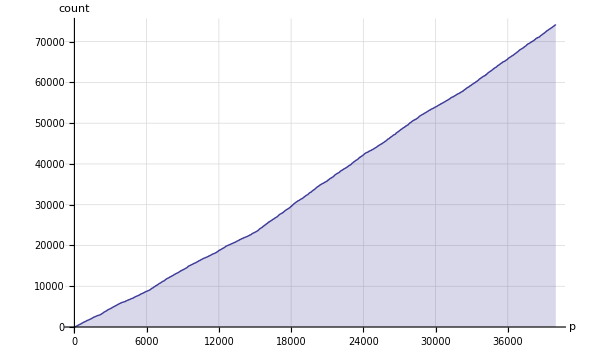

```mathematica
ListPlot[stepFunction , Joined->True,  Filling->Axis, GridLines->Automatic, AxesLabel->{"p","count"}]
```

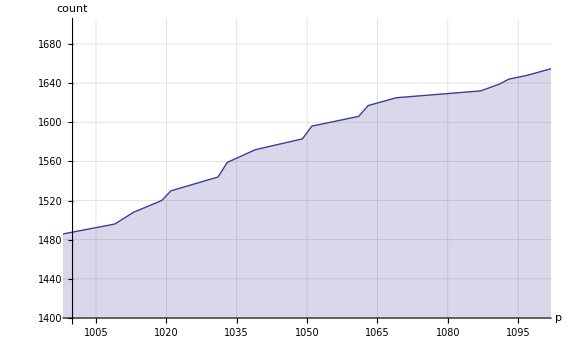

```mathematica
ListPlot[stepFunction , Joined->True, PlotRange->{{1000,1100},{1400,1700}}, Filling->Axis, GridLines->Automatic, AxesLabel->{"p","count"}]
```

```mathematica
InterpolatingPolynomial[Take[myValues,{100,110}], n]
```

802+(9+(1/2+(1/6+(-1/8+(1/40+(1/120+(-37/5040+(3/1120+(-17/25920+(439 (-10+n))/3628800) (-9+n)) (-8+n)) (-7+n)) (-6+n)) (-5+n)) (-4+n)) (-3+n)) (-2+n)) (-1+n)

```mathematica
FindGeneratingFunction[Take[myValues,{100,110}], n]
```

FindGeneratingFunction[{800,809,819,831,843,853,868,882,894,907,920},n]

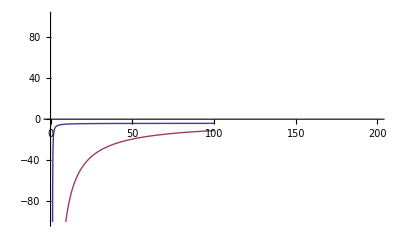

```mathematica
Plot[{3+(n (-8-7 (-2+n) n))/(-1+n)^3,800+(n (809+n (-2417-803 (-3+n) n)))/(-1+n)^4,800+(9+(1/2+(1/6+(-1/8+(1/40+(1/120+(-37/5040+(3/1120+(-17/25920+(439 (-10+n))/3628800) (-9+n)) (-8+n)) (-7+n)) (-6+n)) (-5+n)) (-4+n)) (-3+n)) (-2+n)) (-1+n)}, {n,1,100}, PlotRange->{{0,200},{-100,100}}]
```

```mathematica
Convergents[Take[myValues,{1000,1010}]]
```

{12300,151597501/12325,1870106784636/152041201,23088338514713557/1877100679871,285394954250481062713/23202841655926632,3531191792029540703661506/287088761685880897607,43779716122977199894476414101/3559326490584393024458218,543218721185092888320204049826714/44164123382259910333358466551,6745690123456199610137493785224548553/548430087720230057104038462088536,83835437397532369939881661082974739243398/6815889174351142531948900340194791959,1043248189720582934988087000654031440369393265/84816925434055705387802172937422453226332}

```mathematica
sumInverse = Table[{1/x[[1]]   + 1/3 +1/5, x[[2]]},{x,myData[40]}]
```

{{103/165,3},{119/195,5},{151/255,2},{167/285,3},{199/345,4},{247/435,3},{263/465,3},{311/555,6},{343/615,7},{359/645,3},{391/705,8},{439/795,10},{487/885,5},{503/915,7},{551/1005,5},{583/1065,6},{599/1095,7},{647/1185,4},{679/1245,12},{727/1335,4},{791/1455,5},{823/1515,7},{839/1545,5},{871/1605,7},{887/1635,5},{919/1695,5},{1031/1905,7},{1063/1965,7},{1111/2055,9},{1127/2085,9},{1207/2235,9},{1223/2265,11},«4136»,{317639/595545,24},{317687/595635,26},{317767/595785,26},{317831/595905,18},{317879/595995,25},{318007/596235,27},{318103/596415,12},{318167/596535,21},{318247/596685,25},{318343/596865,12},{318407/596985,18},{318583/597315,17},{318631/597405,14},{318647/597435,14},{318727/597585,13},{318743/597615,27},{318791/597705,22},{318871/597855,18},{318919/597945,28},{318967/598035,18},{319031/598155,20},{319079/598245,24},{319111/598305,25},{319223/598515,30},{319447/598935,31},{319511/599055,22},{319639/599295,23},{319783/599565,23},{319847/599685,25},{319879/599745,29},{319927/599835,27}}

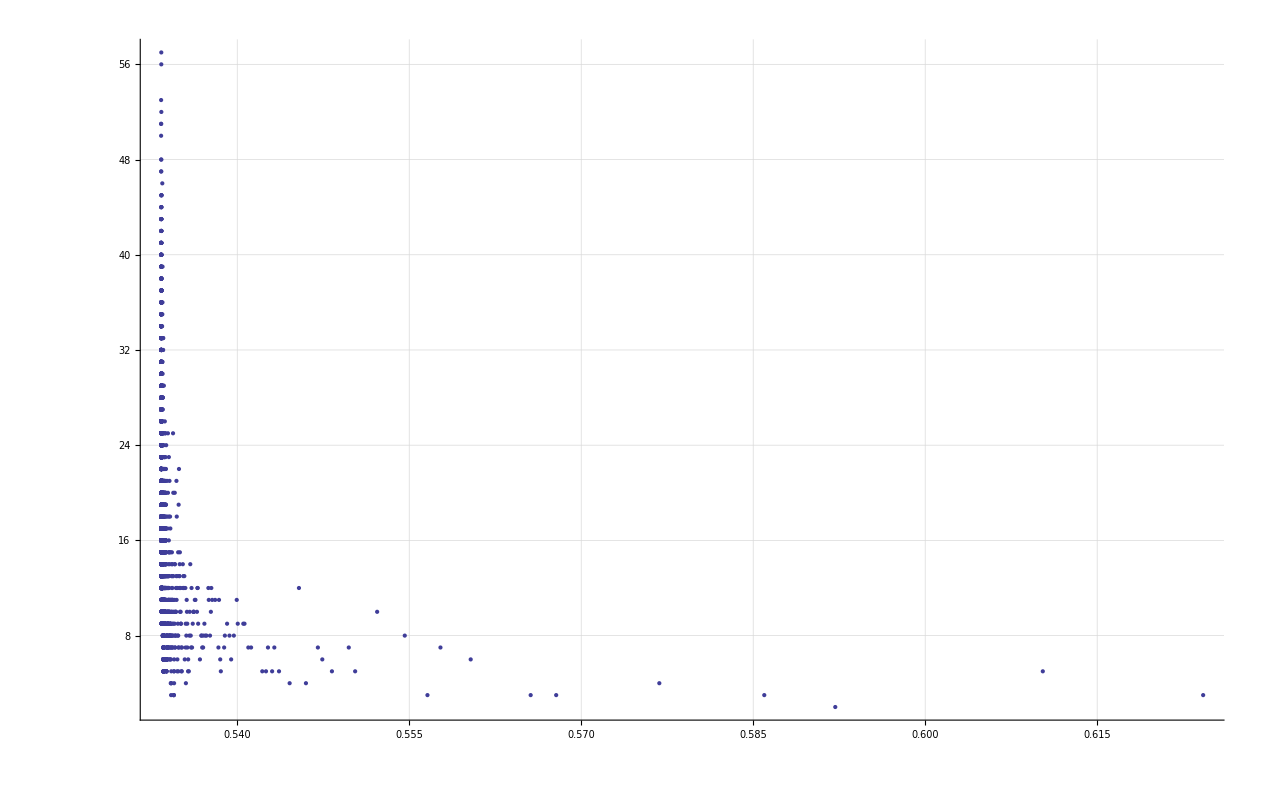

```mathematica
ListPlot[sumInverse, GridLines->Automatic]
```